```mathematica
2+7
```

```mathematica
9
```

```mathematica
%2
```

9

```mathematica
%7-3
```

6

# Practica 0

```mathematica
Expand[(x+y)^2]
```

x^2+2 x y+y^2

```mathematica
2*3
```

6

```mathematica
base=3;
altura=5;
base altura/2
```

15/2

```mathematica
2*(3+5)-3*4
```

4

```mathematica
Sin[Pi]
```

0

```mathematica
{{-1,2},{3,1}} //MatrixForm
```

(-1 | 2
3 | 1)

```mathematica
Head[3]
```

Integer

```mathematica
Head[3.5]
```

Real

```mathematica
Head[3I]
```

Complex

```mathematica
2^500
```

3273390607896141870013189696827599152216642046043064789483291368096133796404674554883270092325904157150886684127560071009217256545885393053328527589376

```mathematica
Sqrt[2]
```

√2

```mathematica
Sqrt[2.]
```

1.41421

```mathematica
N[Sqrt[2],6]
```

1.41421

```mathematica
Sqrt[2]//N
```

1.41421

```mathematica
Sin[Pi/2]
```

1

```mathematica
Sin[90 Degree]
```

1

## 7.-Variables y Funciones Definidas Por El Usuario

```mathematica
a=4
```

4

```mathematica
x=a
```

4

```mathematica
y:=a
y
```

4

```mathematica
f[x_]:=x^2-5*x
f[3]
```

-6

```mathematica
f'[2]
```

-1

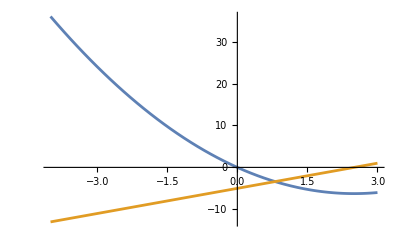

```mathematica
Plot[{f[x],f'[x]},{x,-4,3}]
```

## 8.-Operaciones usuales en Mathematica

```mathematica
Expand[(a+b)^4]
```

a^4+4 a^3 b+6 a^2 b^2+4 a b^3+b^4

2)Simplificar una expresión

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

3)Resolver una ecuacion o despejar una variable en una igualdad
		Solve[expresion1==expresion2,variable]

```mathematica
Solve[x+Sqrt[x+4]==1,x]
```

{{x→1/2 (3-√21)}}

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Solve[a x ^2+b x+c==0,b]
```

{{b→(-c-a x^2)/x}}

## 9.-Otras operaciones con Mathematica